```mathematica
VectorAnalysis`Coordinates
```

VectorAnalysis`Coordinates

```mathematica
VectorAnalysis`Cartesian
```

VectorAnalysis`Cartesian

```mathematica
VectorAnalysis`Coordinates[]
```

VectorAnalysis`Coordinates[]

```mathematica
g[f[x]]==h[x]
```

g[f[x]]==h[x]

```mathematica
FindInstance[g[f[x]]==h[x],{x}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[g[f[x]]==h[x],{x}]

```mathematica
α==β+γ∧{α,β}∈Reals∧γ∈Primes
```

α==β+γ&&(α|β)∈ℝ&&γ∈Primes

```mathematica
Reduce[α==β+γ&&(α|β)∈Reals&&γ∈Primes]
```

γ∈Primes&&β∈ℝ&&γ≥2&&α==β+γ

```mathematica
Reduce[α==β+γ&&(α|β)∈Reals&&γ∈Primes,γ,Primes]
```

(γ|α|β)∈Primes&&(C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥0&&α==4+C[1]+C[2]&&β==2+C[2]&&γ==2+C[1]

```mathematica
x x x - x x + x
```

x-x^2+x^3

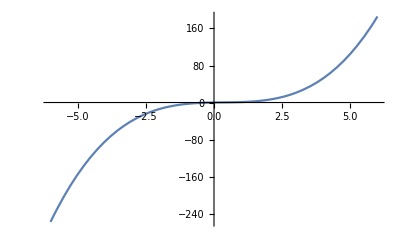

```mathematica
Plot[x-x^2+x^3,{x,-6.,6.}]
```

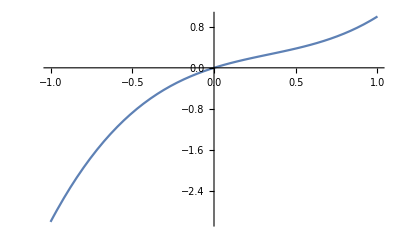

```mathematica
Plot[x-x^2+x^3,{x,-1,1}]
```

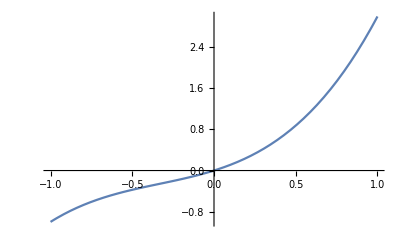

```mathematica
Plot[x+x^2+x^3,{x,-1,1}]
```

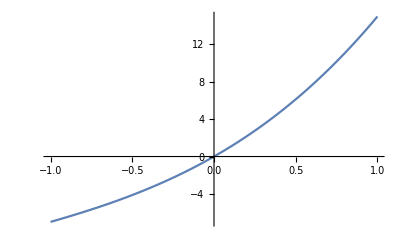

```mathematica
Plot[10x+4 x^2+x^3,{x,-1,1}]
```

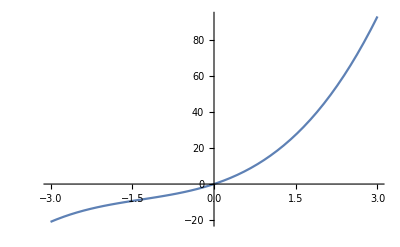

```mathematica
Plot[10x+4 x^2+x^3,{x,-3,3}]
```

```mathematica
(x+1)(x)(x-1)
```

(-1+x) x (1+x)

```mathematica
Expand[(-1+x) x (1+x)]
```

-x+x^3

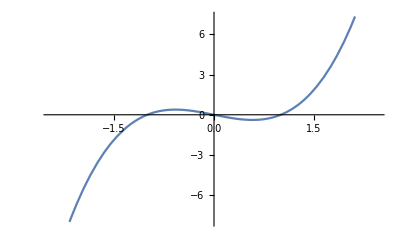

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
f[x_]:=-x+x^3
```

```mathematica
FullSimplify[
1
,{x,x
```

```mathematica
f[x_Real]:=-x+x^3
```

```mathematica
f[4]
```

60

```mathematica
FullSimplify[
Normalize[{x,a}].Normalize[{x,f[x]}]
,{x,a}∈Reals]
```

((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))

```mathematica
Manipulate[Plot[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))),{x,-1.3153266657381688,1.3153266657381688}],{a,-1.5531229146464538,1.5531229146464538}]
```

```mathematica
Manipulate[
Plot[{
a,
f[x],
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))
},{x,-3,-3}
],{a,-10,10}]
```

Plot::plld: Endpoints for x in {x,-3,-3} must have distinct machine-precision numerical values.

```mathematica
Manipulate[
Plot[{
a,
f[x],
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))
},{x,-3,3}
],{a,-10,10}]
```

```mathematica
Manipulate[
Plot[{
a,
f[x],
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))
},{x,-3,3}
,PlotRange->{-10,10}],{a,-10,10}]
```

```mathematica
∫_-b^b (((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))))ⅆx
```

$Aborted

```mathematica
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))/.a->0
```

(x Sign[x])/(√(x^2 (2-2 x^2+x^4)))

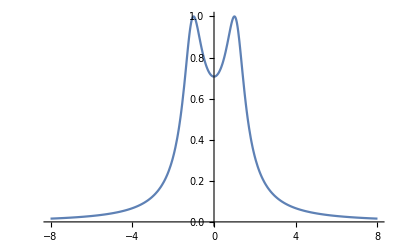

```mathematica
Plot[(x Sign[x])/(√(x^2 (2-2 x^2+x^4))),{x,-8,8}]
```

```mathematica
Limit[∫_-b^b ((x Sign[x])/(√(x^2 (2-2 x^2+x^4))))ⅆx,b->∞]
```

$Aborted

```mathematica
Integrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),x]
```

∫(x Sign[x])/(√(x^2 (2-2 x^2+x^4)))ⅆx

```mathematica
NIntegrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),x]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in x.

NIntegrate[(x Sign[x])/(√(x^2 (2-2 x^2+x^4))),x]

```mathematica
2 NIntegrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),{x,0,100}]
```

4.01646

```mathematica
2 NIntegrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),{x,0,10}]
```

3.83579

```mathematica
2 NIntegrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),{x,0,1000}]
```

4.03446

```mathematica
2 NIntegrate[((x Sign[x])/(√(x^2 (2-2 x^2+x^4)))),{x,0,10000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.37761}. NIntegrate obtained 2.01813 and 0.0000283915 for the integral and error estimates.

4.03626

```mathematica
GenomeLookup["CTCTCTAACTAAACT"]
```

{{{Chromosome1,1},{108939073,108939087}},{{Chromosome1,-1},{138309610,138309624}},{{Chromosome5,-1},{139640264,139640278}},{{Chromosome8,1},{72019948,72019962}},{{Chromosome9,1},{110092060,110092074}}}

```mathematica
FullSimplify[
Normalize[{x,x}].Normalize[{x,f[x]}]
,{x,a}∈Reals]
```

x^2/(√2 √(2-2 x^2+x^4))

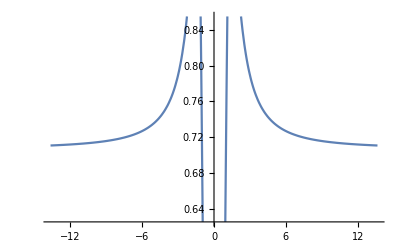

```mathematica
Plot[x^2/(√2 √(2-2 x^2+x^4)),{x,-13.649999999999999,13.649999999999999}]
```

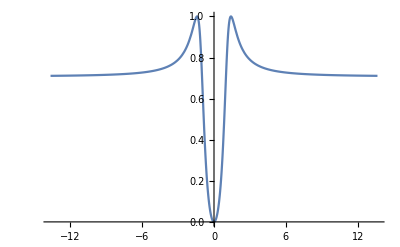

```mathematica
Plot[x^2/(√2 √(2-2 x^2+x^4)),{x,-13.649999999999999,13.649999999999999},PlotRange->Full]
```

```mathematica
D[x^2/(√2 √(2-2 x^2+x^4)),x]
```

-(x^2 (-4 x+4 x^3))/(2 √2 (2-2 x^2+x^4)^(3/2))+(√2 x)/(√(2-2 x^2+x^4))

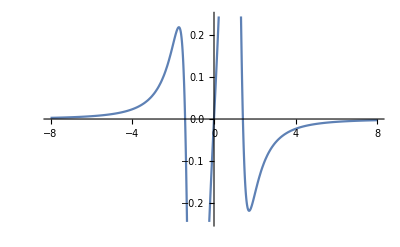

```mathematica
Plot[-(x^2 (-4 x+4 x^3))/(2 √2 (2-2 x^2+x^4)^(3/2))+(√2 x)/(√(2-2 x^2+x^4)),{x,-8,8}]
```

```mathematica
Reduce[-(x^2 (-4 x+4 x^3))/(2 √2 (2-2 x^2+x^4)^(3/2))+(√2 x)/(√(2-2 x^2+x^4))==0,x,Reals]
```

x==0||x==-√2||x==√2

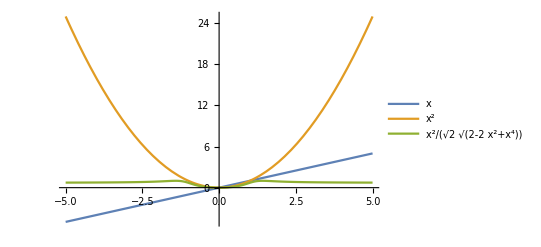

```mathematica
Plot[{x,x^2,x^2/(√2 √(2-2 x^2+x^4))},{x,-5,5},PlotRange->Full,PlotLegends->"Expressions"]
```

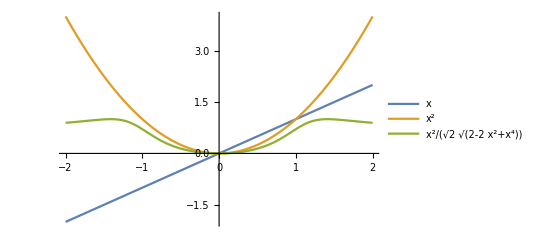

```mathematica
Plot[{x,x^2,x^2/(√2 √(2-2 x^2+x^4))},{x,-2,2},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
(G Subscript[m, 1] Subscript[m, 2])/r^2∧{G,Subscript[m, 1],Subscript[m, 2],r}∈Reals
```

(G m_1 m_2)/r^2&&(G|m_1|m_2|r)∈ℝ

```mathematica
F[r]==(G Subscript[m, 1] Subscript[m, 2])/r^2∧{G,Subscript[m, 1],Subscript[m, 2],r}∈Reals
```

F[r]==(G m_1 m_2)/r^2&&(G|m_1|m_2|r)∈ℝ

```mathematica
2F[r]==F[k+r]
```

2 F[r]==F[k+r]

```mathematica
2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2&&(G|Subscript[m, 1]|Subscript[m, 2]|r)∈Reals
```

(2 G m_1 m_2)/r^2==(G m_1 m_2)/(k+r)^2&&(G|m_1|m_2|r)∈ℝ

```mathematica
Solve[2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2&&(G|Subscript[m, 1]|Subscript[m, 2]|r|k)∈Reals,k,Reals]
```

{{k→-r-(√(r^2))/(√2)},{k→-r+(√(r^2))/(√2)}}

```mathematica
-r-(√(r^2))/(√2)
```

-r-(√(r^2))/(√2)

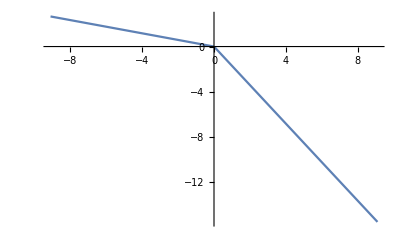

```mathematica
Plot[-r-(√(r^2))/(√2),{r,-9.100000000000001,9.100000000000001}]
```

```mathematica
-r+(√(r^2))/(√2)
```

-r+(√(r^2))/(√2)

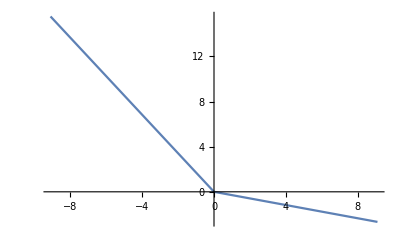

```mathematica
Plot[-r+(√(r^2))/(√2),{r,-9.100000000000001,9.100000000000001}]
```

```mathematica
Dt[F[x[t]]]
```

Dt[t] F'[x[t]] x'[t]

```mathematica
Dt[h[g[x]]]
```

Dt[x] g'[x] h'[g[x]]

```mathematica
Dt[Dt[h[g[x]]]]
```

Dt[Dt[x]] g'[x] h'[g[x]]+Dt[x]^2 h'[g[x]] g''[x]+Dt[x]^2 g'[x]^2 h''[g[x]]

```mathematica
Nest[Dt,g[x],1]
```

Dt[x] g'[x]

```mathematica
Nest[Dt,g[x],2]
```

Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x]

```mathematica
Nest[Dt,g[x],3]
```

Dt[Dt[Dt[x]]] g'[x]+3 Dt[x] Dt[Dt[x]] g''[x]+Dt[x]^3 g^(3)[x]

```mathematica
NestList[Dt,g[x],3]
```

{g[x],Dt[x] g'[x],Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x],Dt[Dt[Dt[x]]] g'[x]+3 Dt[x] Dt[Dt[x]] g''[x]+Dt[x]^3 g^(3)[x]}

```mathematica
Grid@NestList[Dt,g[x],3]
```

Grid[{g[x],Dt[x] g'[x],Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x],Dt[Dt[Dt[x]]] g'[x]+3 Dt[x] Dt[Dt[x]] g''[x]+Dt[x]^3 g^(3)[x]}]

```mathematica
Column@NestList[Dt,g[x],3]
```

g[x]
Dt[x] g'[x]
Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x]
Dt[Dt[Dt[x]]] g'[x]+3 Dt[x] Dt[Dt[x]] g''[x]+Dt[x]^3 g^(3)[x]

```mathematica
Column@NestList[Dt,g[x],10]
```

g[x]
Dt[x] g'[x]
Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x]
Dt[Dt[Dt[x]]] g'[x]+3 Dt[x] Dt[Dt[x]] g''[x]+Dt[x]^3 g^(3)[x]
Dt[Dt[Dt[Dt[x]]]] g'[x]+3 Dt[Dt[x]]^2 g''[x]+4 Dt[x] Dt[Dt[Dt[x]]] g''[x]+6 Dt[x]^2 Dt[Dt[x]] g^(3)[x]+Dt[x]^4 g^(4)[x]
Dt[Dt[Dt[Dt[Dt[x]]]]] g'[x]+10 Dt[Dt[x]] Dt[Dt[Dt[x]]] g''[x]+5 Dt[x] Dt[Dt[Dt[Dt[x]]]] g''[x]+15 Dt[x] Dt[Dt[x]]^2 g^(3)[x]+10 Dt[x]^2 Dt[Dt[Dt[x]]] g^(3)[x]+10 Dt[x]^3 Dt[Dt[x]] g^(4)[x]+Dt[x]^5 g^(5)[x]
Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g'[x]+10 Dt[Dt[Dt[x]]]^2 g''[x]+15 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g''[x]+6 Dt[x] Dt[Dt[Dt[Dt[Dt[x]]]]] g''[x]+15 Dt[Dt[x]]^3 g^(3)[x]+60 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(3)[x]+15 Dt[x]^2 Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+45 Dt[x]^2 Dt[Dt[x]]^2 g^(4)[x]+20 Dt[x]^3 Dt[Dt[Dt[x]]] g^(4)[x]+15 Dt[x]^4 Dt[Dt[x]] g^(5)[x]+Dt[x]^6 g^(6)[x]
Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g'[x]+35 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g''[x]+21 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[x]]]]] g''[x]+7 Dt[x] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g''[x]+105 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]] g^(3)[x]+70 Dt[x] Dt[Dt[Dt[x]]]^2 g^(3)[x]+105 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+21 Dt[x]^2 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+105 Dt[x] Dt[Dt[x]]^3 g^(4)[x]+210 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(4)[x]+35 Dt[x]^3 Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+105 Dt[x]^3 Dt[Dt[x]]^2 g^(5)[x]+35 Dt[x]^4 Dt[Dt[Dt[x]]] g^(5)[x]+21 Dt[x]^5 Dt[Dt[x]] g^(6)[x]+Dt[x]^7 g^(7)[x]
Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g'[x]+35 Dt[Dt[Dt[Dt[x]]]]^2 g''[x]+56 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g''[x]+28 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g''[x]+8 Dt[x] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g''[x]+280 Dt[Dt[x]] Dt[Dt[Dt[x]]]^2 g^(3)[x]+210 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+280 Dt[x] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+168 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+28 Dt[x]^2 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+105 Dt[Dt[x]]^4 g^(4)[x]+840 Dt[x] Dt[Dt[x]]^2 Dt[Dt[Dt[x]]] g^(4)[x]+280 Dt[x]^2 Dt[Dt[Dt[x]]]^2 g^(4)[x]+420 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+56 Dt[x]^3 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+420 Dt[x]^2 Dt[Dt[x]]^3 g^(5)[x]+560 Dt[x]^3 Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(5)[x]+70 Dt[x]^4 Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+210 Dt[x]^4 Dt[Dt[x]]^2 g^(6)[x]+56 Dt[x]^5 Dt[Dt[Dt[x]]] g^(6)[x]+28 Dt[x]^6 Dt[Dt[x]] g^(7)[x]+Dt[x]^8 g^(8)[x]
Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]] g'[x]+126 Dt[Dt[Dt[Dt[x]]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g''[x]+84 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g''[x]+36 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g''[x]+9 Dt[x] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g''[x]+280 Dt[Dt[Dt[x]]]^3 g^(3)[x]+1260 Dt[Dt[x]] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+315 Dt[x] Dt[Dt[Dt[Dt[x]]]]^2 g^(3)[x]+378 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+504 Dt[x] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+252 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+36 Dt[x]^2 Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g^(3)[x]+1260 Dt[Dt[x]]^3 Dt[Dt[Dt[x]]] g^(4)[x]+2520 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[x]]]^2 g^(4)[x]+1890 Dt[x] Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+1260 Dt[x]^2 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+756 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+84 Dt[x]^3 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(4)[x]+945 Dt[x] Dt[Dt[x]]^4 g^(5)[x]+3780 Dt[x]^2 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]] g^(5)[x]+840 Dt[x]^3 Dt[Dt[Dt[x]]]^2 g^(5)[x]+1260 Dt[x]^3 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+126 Dt[x]^4 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(5)[x]+1260 Dt[x]^3 Dt[Dt[x]]^3 g^(6)[x]+1260 Dt[x]^4 Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(6)[x]+126 Dt[x]^5 Dt[Dt[Dt[Dt[x]]]] g^(6)[x]+378 Dt[x]^5 Dt[Dt[x]]^2 g^(7)[x]+84 Dt[x]^6 Dt[Dt[Dt[x]]] g^(7)[x]+36 Dt[x]^7 Dt[Dt[x]] g^(8)[x]+Dt[x]^9 g^(9)[x]
Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]]] g'[x]+126 Dt[Dt[Dt[Dt[Dt[x]]]]]^2 g''[x]+210 Dt[Dt[Dt[Dt[x]]]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g''[x]+120 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g''[x]+45 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g''[x]+10 Dt[x] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]] g''[x]+2100 Dt[Dt[Dt[x]]]^2 Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+1575 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]]^2 g^(3)[x]+2520 Dt[Dt[x]] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+1260 Dt[x] Dt[Dt[Dt[Dt[x]]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+630 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+840 Dt[x] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+360 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g^(3)[x]+45 Dt[x]^2 Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g^(3)[x]+6300 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]]^2 g^(4)[x]+2800 Dt[x] Dt[Dt[Dt[x]]]^3 g^(4)[x]+3150 Dt[Dt[x]]^3 Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+12600 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+1575 Dt[x]^2 Dt[Dt[Dt[Dt[x]]]]^2 g^(4)[x]+3780 Dt[x] Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+2520 Dt[x]^2 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+1260 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(4)[x]+120 Dt[x]^3 Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g^(4)[x]+945 Dt[Dt[x]]^5 g^(5)[x]+12600 Dt[x] Dt[Dt[x]]^3 Dt[Dt[Dt[x]]] g^(5)[x]+12600 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[x]]]^2 g^(5)[x]+9450 Dt[x]^2 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+4200 Dt[x]^3 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+2520 Dt[x]^3 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(5)[x]+210 Dt[x]^4 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(5)[x]+4725 Dt[x]^2 Dt[Dt[x]]^4 g^(6)[x]+12600 Dt[x]^3 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]] g^(6)[x]+2100 Dt[x]^4 Dt[Dt[Dt[x]]]^2 g^(6)[x]+3150 Dt[x]^4 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g^(6)[x]+252 Dt[x]^5 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(6)[x]+3150 Dt[x]^4 Dt[Dt[x]]^3 g^(7)[x]+2520 Dt[x]^5 Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(7)[x]+210 Dt[x]^6 Dt[Dt[Dt[Dt[x]]]] g^(7)[x]+630 Dt[x]^6 Dt[Dt[x]]^2 g^(8)[x]+120 Dt[x]^7 Dt[Dt[Dt[x]]] g^(8)[x]+45 Dt[x]^8 Dt[Dt[x]] g^(9)[x]+Dt[x]^10 g^(10)[x]

```mathematica
F[x]==m a[x]
```

F[x]==m a[x]

```mathematica
Dt[F[x]==m a[x]]
```

Dt[x] F'[x]==a[x] Dt[m]+m Dt[x] a'[x]

```mathematica
Nest[Dt,g[x],10]
```

Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]]] g'[x]+126 Dt[Dt[Dt[Dt[Dt[x]]]]]^2 g''[x]+210 Dt[Dt[Dt[Dt[x]]]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g''[x]+120 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g''[x]+45 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g''[x]+10 Dt[x] Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]]] g''[x]+2100 Dt[Dt[Dt[x]]]^2 Dt[Dt[Dt[Dt[x]]]] g^(3)[x]+1575 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]]^2 g^(3)[x]+2520 Dt[Dt[x]] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+1260 Dt[x] Dt[Dt[Dt[Dt[x]]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(3)[x]+630 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+840 Dt[x] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(3)[x]+360 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g^(3)[x]+45 Dt[x]^2 Dt[Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]]] g^(3)[x]+6300 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]]^2 g^(4)[x]+2800 Dt[x] Dt[Dt[Dt[x]]]^3 g^(4)[x]+3150 Dt[Dt[x]]^3 Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+12600 Dt[x] Dt[Dt[x]] Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(4)[x]+1575 Dt[x]^2 Dt[Dt[Dt[Dt[x]]]]^2 g^(4)[x]+3780 Dt[x] Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+2520 Dt[x]^2 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(4)[x]+1260 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(4)[x]+120 Dt[x]^3 Dt[Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]]] g^(4)[x]+945 Dt[Dt[x]]^5 g^(5)[x]+12600 Dt[x] Dt[Dt[x]]^3 Dt[Dt[Dt[x]]] g^(5)[x]+12600 Dt[x]^2 Dt[Dt[x]] Dt[Dt[Dt[x]]]^2 g^(5)[x]+9450 Dt[x]^2 Dt[Dt[x]]^2 Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+4200 Dt[x]^3 Dt[Dt[Dt[x]]] Dt[Dt[Dt[Dt[x]]]] g^(5)[x]+2520 Dt[x]^3 Dt[Dt[x]] Dt[Dt[Dt[Dt[Dt[x]]]]] g^(5)[x]+210 Dt[x]^4 Dt[Dt[Dt[Dt[Dt[Dt[x]]]]]] g^(5)[x]+4725 Dt[x]^2 Dt[Dt[x]]^4 g^(6)[x]+12600 Dt[x]^3 Dt[Dt[x]]^2 Dt[Dt[Dt[x]]] g^(6)[x]+2100 Dt[x]^4 Dt[Dt[Dt[x]]]^2 g^(6)[x]+3150 Dt[x]^4 Dt[Dt[x]] Dt[Dt[Dt[Dt[x]]]] g^(6)[x]+252 Dt[x]^5 Dt[Dt[Dt[Dt[Dt[x]]]]] g^(6)[x]+3150 Dt[x]^4 Dt[Dt[x]]^3 g^(7)[x]+2520 Dt[x]^5 Dt[Dt[x]] Dt[Dt[Dt[x]]] g^(7)[x]+210 Dt[x]^6 Dt[Dt[Dt[Dt[x]]]] g^(7)[x]+630 Dt[x]^6 Dt[Dt[x]]^2 g^(8)[x]+120 Dt[x]^7 Dt[Dt[Dt[x]]] g^(8)[x]+45 Dt[x]^8 Dt[Dt[x]] g^(9)[x]+Dt[x]^10 g^(10)[x]

```mathematica
Nest[Dt,g[x],10]/.Dt[x]->1
```

g^(10)[x]

```mathematica
Nest[Dt,g[x],2]
```

Dt[Dt[x]] g'[x]+Dt[x]^2 g''[x]

```mathematica
Nest[Dt,g[x],1]
```

Dt[x] g'[x]

```mathematica
Nest[Dt,g[x],10]/.Dt[x]->0
```

0

```mathematica
f[x]==x+2
```

-x+x^3==2+x

```mathematica
f
```

f

```mathematica
ClearAll[f]
```

```mathematica
x x x x x x x x x x x
```

x^11

```mathematica
{{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
Solve[(y-Subscript[y, 1])==(x-Subscript[x, 1])m,y,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[y-y_1==m (x-x_1),y,ℝ]

```mathematica
Reduce[(y-Subscript[y, 1])==(x-Subscript[x, 1])m,y,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[y-y_1==m (x-x_1),y,ℝ]

```mathematica
Reduce[(y-yy)==(x-Subscript[x, 1])m,y,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[y-yy==m (x-x_1),y,ℝ]

```mathematica
Solve[y-yy==m (x-xx),y,Reals]
```

{{y→m x-m xx+yy}}

```mathematica
y==(x-Subscript[x, 1])m+yy
```

y==yy+m (x-x_1)

```mathematica
y==Subscript[y, 1]+m (x-Subscript[x, 1])/.{Subscript[x, 1]->0,Subscript[y, 1]->0,m->1}
```

y==x

```mathematica
y==Subscript[y, 1]+m (x-Subscript[x, 1])/.{Subscript[x, 1]->0,Subscript[y, 1]->0,m->2}
```

y==2 x

```mathematica
Dt[y==2 x]
```

Dt[y]==2 Dt[x]

```mathematica
Dt[y==x]
```

Dt[y]==Dt[x]

```mathematica
Dt[Dt[y]==2 Dt[x]]
```

Dt[Dt[y]]==2 Dt[Dt[x]]

```mathematica
Dt[α β]
```

β Dt[α]+α Dt[β]

```mathematica
D[F[x,y,z], x]==D[F[x,y,z], {y,z}]
```

F^(1,0,0)[x,y,z]==F^(0,z,0)[x,y,z]

```mathematica
D[F[x,y,z], y]==D[D[F[x,y,z],z],x]
```

F^(0,1,0)[x,y,z]==F^(1,0,1)[x,y,z]

```mathematica
DSolve[Derivative[0,1,0][F][x,y,z]==Derivative[1,0,1][F][x,y,z],{F[x,y,z],F[x,y,z]},{x,y,z}]
```

DSolve[F^(0,1,0)[x,y,z]==F^(1,0,1)[x,y,z],{F[x,y,z],F[x,y,z]},{x,y,z}]

```mathematica
DSolve[Derivative[0,1,0][F][x,y,z]==Derivative[1,0,1][F][x,y,z],{F[x,y,z]},{x,y,z}]
```

DSolve[F^(0,1,0)[x,y,z]==F^(1,0,1)[x,y,z],{F[x,y,z]},{x,y,z}]

```mathematica
D[F[x,y,z], y]==D[F[x,y,z], {x,z}]
```

F^(0,1,0)[x,y,z]==F^(z,0,0)[x,y,z]

```mathematica
D[F[x,y,z], y]==D[F[x,y,z], {z,x}]
```

F^(0,1,0)[x,y,z]==F^(0,0,x)[x,y,z]

```mathematica
(F^(0,1,0))[x,y,z]
```

```mathematica
D[F[x,y,z], y]==D[D[F[x,y,z], z], x]
```

F^(0,1,0)[x,y,z]==F^(1,0,1)[x,y,z]

```mathematica
Dt[D[F[x,y,z], y]==D[D[F[x,y,z], z], x]]
```

Dt[z] F^(0,1,1)[x,y,z]+Dt[y] F^(0,2,0)[x,y,z]+Dt[x] F^(1,1,0)[x,y,z]==Dt[z] F^(1,0,2)[x,y,z]+Dt[y] F^(1,1,1)[x,y,z]+Dt[x] F^(2,0,1)[x,y,z]

```mathematica
D[F[x,y,z], y]==D[D[F[x,y,z], z], x]/.z->y'
```

```mathematica
(1-a)p+a q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

F^(0,1,0)[x,y,y']==F^(1,0,1)[x,y,y']

```mathematica
(1-a)p+a q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

{a t+(1-a) Cos[t],a t+(1-a) Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{a t+(1-a) Cos[t],a t+(1-a) Sin[t]}
},{t,0,2π}
],{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{a t+(1-a) Cos[t],a t+(1-a) Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1}]
```

```mathematica
ExpandAll[(1-a)p+a q]
```

p-a p+a q

```mathematica
(1-a){x[t],y[t]}+ a{p[t],q[t]}
```

{a p[t]+(1-a) x[t],a q[t]+(1-a) y[t]}

```mathematica
a({x[t],y[t]}-{p[t],q[t]})
```

{a (-p[t]+x[t]),a (-q[t]+y[t])}

```mathematica
{x[t],y[t]}+a({x[t],y[t]}-{p[t],q[t]})
```

{x[t]+a (-p[t]+x[t]),y[t]+a (-q[t]+y[t])}

```mathematica
ExpandAll[{x[t],y[t]}+a({x[t],y[t]}-{p[t],q[t]})]
```

{-a p[t]+x[t]+a x[t],-a q[t]+y[t]+a y[t]}

```mathematica
ExpandAll[(1-a){x[t],y[t]}+ a{p[t],q[t]}]
```

{a p[t]+x[t]-a x[t],a q[t]+y[t]-a y[t]}

```mathematica
{-a p[t]+x[t]+a x[t],-a q[t]+y[t]+a y[t]}=={a p[t]+x[t]-a x[t],a q[t]+y[t]-a y[t]}
```

{-a p[t]+x[t]+a x[t],-a q[t]+y[t]+a y[t]}=={a p[t]+x[t]-a x[t],a q[t]+y[t]-a y[t]}

```mathematica
Reduce[{-a p[t]+x[t]+a x[t],-a q[t]+y[t]+a y[t]}=={a p[t]+x[t]-a x[t],a q[t]+y[t]-a y[t]}]
```

(q[t]==y[t]&&p[t]==x[t])||a==0

```mathematica
p+a(p-q)
```

p+a (p-q)

```mathematica
Expand[p+a (p-q)]
```

p+a p-a q

```mathematica
ExpandAll[(1-a)p+a q]
```

p-a p+a q

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{a t+(1-a) Cos[t],a t+(1-a) Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1}]
```

```mathematica
p+a p-a q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

{-a t+Cos[t]+a Cos[t],-a t+Sin[t]+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{-a t+Cos[t]+a Cos[t],-a t+Sin[t]+a Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1}]
```

```mathematica
Expand[q+a (p-q)]
```

a p+q-a q

```mathematica
a p+q-a q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

{t-a t+a Cos[t],t-a t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{t-a t+a Cos[t],t-a t+a Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1}]
```

```mathematica
Sin[t]
```

Sin[t]

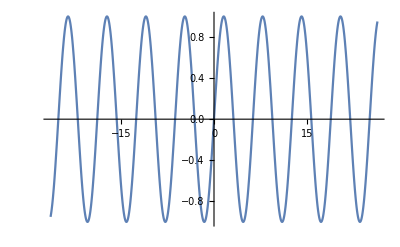

```mathematica
Plot[Sin[t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
Sin[π/2]
```

1

```mathematica
(1-Sin[t])p+Sin[t]q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

{Cos[t] (1-Sin[t])+t Sin[t],t Sin[t]+(1-Sin[t]) Sin[t]}

```mathematica
Sin[t]
```

Sin[t]

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{t-a t+a Cos[t],t-a t+a Sin[t]},
{Cos[t] (1-Sin[b])+t Sin[b],t Sin[b]+(1-Sin[t]) Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1}]
```

```mathematica
(1-Sin[b])p+Sin[b]q/.{p->{Cos[t],Sin[t]},q->{t,t}}
```

{Cos[t] (1-Sin[b])+t Sin[b],t Sin[b]+(1-Sin[b]) Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{t-a t+a Cos[t],t-a t+a Sin[t]},
{Cos[t] (1-Sin[b])+t Sin[b],t Sin[b]+(1-Sin[b]) Sin[t]}
},{t,0,2π}
,PlotRange->{{-2,2π},{-2,2π}}],{a,0,1},{b,0,π/2}]
```

```mathematica
(1-a)p+a q ==q+a(p-q)
```

(1-a) p+a q==a (p-q)+q

```mathematica
Reduce[(1-a) p+a q==a (p-q)+q]
```

a==1/2||p==q

```mathematica
(1-a)p+a q ==p+a(p-q)
```

(1-a) p+a q==p+a (p-q)

```mathematica
Reduce[(1-a) p+a q==p+a (p-q)]
```

a==0||p==q

```mathematica
(1-a)p+a q ==p+a(q-p)
```

(1-a) p+a q==p+a (-p+q)

```mathematica
Solve[(1-a)p+a q ==p+a k,k]
```

{{k→-p+q}}

```mathematica
(1-a) p+a q==p+a (q-p)
```

(1-a) p+a q==p+a (-p+q)

```mathematica
ExpandAll[(1-a) p+a q==p+a (q-p)]
```

True

```mathematica
f[a]:=(1-a) p+a q
```

```mathematica
f[1]
```

f[1]

```mathematica
f[a_]:=(1-a) p+a q
```

```mathematica
f[1]
```

q

```mathematica
f[0]
```

p

```mathematica
InverseFunction[f]
```

(p-#1)/(p-q)&

```mathematica
Dt[(1-a)p+a q]
```

-p Dt[a]+q Dt[a]+(1-a) Dt[p]+a Dt[q]

```mathematica
Dt[(1-a)p+a q]/.Dt[a]->1
```

-p+q+(1-a) Dt[p]+a Dt[q]

```mathematica
ClearAll[f]
```

```mathematica
(1-a)p+a q
```

```mathematica
Curl
```

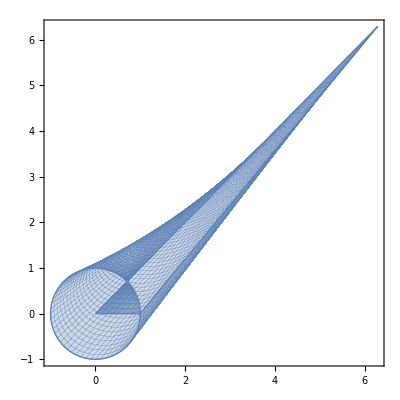

```mathematica
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
Curl[{t-a t+a Cos[t],t-a t+a Sin[t]},{t,a}]
```

1-a+t-Cos[t]+a Cos[t]

```mathematica
Manipulate[Plot[1-a+t-Cos[t]+a Cos[t],{t,0,2π}],{a,0,1}]
```

```mathematica
Plot3D[1-a+t-Cos[t]+a Cos[t],{t,0,2π},{a,0,1}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}]
,{b,0.001,1}]
```

```mathematica
{x==1,x==2}
```

{x==1,x==2}

```mathematica
(1-a)p+a q/.{p-> {t,2},q->{t,3}}
```

{(1-a) t+a t,2 (1-a)+3 a}

```mathematica
Manipulate[
ParametricPlot[{
{t,2},
{t,3},
{(1-a) t+a t,2 (1-a)+3 a}
},{t,0,1},PlotRange->{{0,1},{0,3}}
,{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,2},
{t,3},
{(1-a) t+a t,2 (1-a)+3 a}
},{t,0,1},PlotRange->{{0,1},{0,3}}]
,{a,0,1}]
```

```mathematica
Curl[{(1-a) t+a t,2 (1-a)+3 a},{t,a}]
```

0

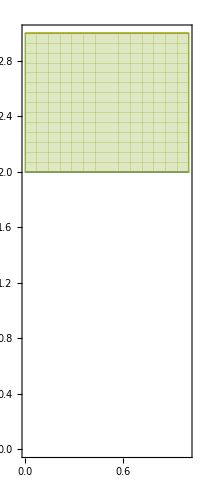

```mathematica
ParametricPlot[{
{t,2},
{t,3},
{(1-a) t+a t,2 (1-a)+3 a}
},{t,0,1},{a,0,1}
,PlotRange->{{0,1},{0,3}}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,2},
{t,3},
{(1-a) t+a t,2 (1-a)+3 a}
},{t,0,2π},{a,0,b}]
,{b,0.001,1}]
```

```mathematica
(p.q).q==a
```

p.q.q==a

```mathematica
({a,b}.{c.d}).{c.d}==a
```

{a,b}.(c.d)^2==a

```mathematica
{a c c,b d d}
```

{a c^2,b d^2}

```mathematica
({b,c}.{d.e}).{d.e}==a
```

{b,c}.(d.e)^2==a

```mathematica
b d d+c e e
```

b d^2+c e^2

```mathematica
b d d+c e e==a
```

b d^2+c e^2==a

```mathematica
(p.q).q==a Norm[q]
```

p.q.q==a Norm[q]

```mathematica
FullSimplify[Normalize[{a,b}],{a,b}∈Reals]
```

{a/(√(a^2+b^2)),b/(√(a^2+b^2))}

```mathematica
FullSimplify[Normalize[{b,c}],{a,b}∈Reals]
```

{b/(√(b^2+Abs[c]^2)),c/(√(b^2+Abs[c]^2))}

```mathematica
FullSimplify[Normalize[{b,c}],{b,c}∈Reals]
```

{b/(√(b^2+c^2)),c/(√(b^2+c^2))}

```mathematica
{b/(√(b^2+c^2)),c/(√(b^2+c^2))}
```

```mathematica
FullSimplify[Normalize[{d,e}],{d,e}∈Reals]
```

{d/(√(d^2+e^2)),e/(√(d^2+e^2))}

```mathematica
b/(√(b^2+c^2)) d/(√(d^2+e^2)) d/(√(d^2+e^2))+c/(√(b^2+c^2))e/(√(d^2+e^2)) e/(√(d^2+e^2))==a
```

(b d^2)/(√(b^2+c^2) (d^2+e^2))+(c e^2)/(√(b^2+c^2) (d^2+e^2))==a

```mathematica
With[{b=t,c=2,d=t,e=3},(b d^2)/(√(b^2+c^2) (d^2+e^2))+(c e^2)/(√(b^2+c^2) (d^2+e^2))==a]
```

18/(√(4+t^2) (9+t^2))+t^3/(√(4+t^2) (9+t^2))==a

```mathematica
((1-a)p).(a q)
```

((1-a) p).(a q)

```mathematica
((1-a)p).(a q)/.{p->{t,2},q->{t,3}}
```

6 (1-a) a+(1-a) a t^2

```mathematica
Simplify[6 (1-a) a+(1-a) a t^2]
```

-(-1+a) a (6+t^2)

```mathematica
Manipulate[Plot[-(-1+a) a (6+t^2),{t,-2.2882456112707374,2.2882456112707374}],{a,0,1}]
```

```mathematica
((1-a)Normalize[p]).(a Normalize[q])/.{p->{t,2},q->{t,3}}
```

(6 (1-a) a)/(√(4+Abs[t]^2) √(9+Abs[t]^2))+((1-a) a t^2)/(√(4+Abs[t]^2) √(9+Abs[t]^2))

```mathematica
((1-a)Normalize[p]).(a Normalize[q])/.{p->{t,2},q->{t,3}}∧Element[t,Reals]
```

((1-a) Normalize[p]).(a Normalize[q])/.{p→{t,2},q→{t,3}}&&t∈ℝ

```mathematica
FullSimplify[((1-a)Normalize[p]).(a Normalize[q])/.{p->{t,2},q->{t,3}},Element[t,Reals]]
```

-((-1+a) a (6+t^2))/(√((4+t^2) (9+t^2)))

```mathematica
-((-1+a) a (6+t^2))/(√((4+t^2) (9+t^2)))
```

-((-1+a) a (6+t^2))/(√((4+t^2) (9+t^2)))

```mathematica
Manipulate[Plot[-((-1+a) a (6+t^2))/(√((4+t^2) (9+t^2))),{t,-2.6326307122076757,2.632630713647842}],{a,0,1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
{a/(√2)+π/4-(a π)/4,a/(√2)+π/4-(a π)/4}
}]
,{b,0.001,1}]
```

```mathematica
{t-a t+a Cos[t],t-a t+a Sin[t]}/.t->1
```

{1-a+a Cos[1],1-a+a Sin[1]}

```mathematica
{t-a t+a Cos[t],t-a t+a Sin[t]}/.t->π/4
```

{a/(√2)+π/4-(a π)/4,a/(√2)+π/4-(a π)/4}

```mathematica
N@(π/4)
```

0.785398

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->π/4
```

{b/(√2)+π/4-(b π)/4,b/(√2)+π/4-(b π)/4}

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
ListPlot[{{b/(√2)+π/4-(b π)/4,b/(√2)+π/4-(b π)/4}}]
}]
,{b,0.001,1}]
```

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->.5
```

{0.5+0.377583 b,0.5-0.0205745 b}

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
ListPlot[{{0.5+0.37758256189037276 b,0.5-0.020574461395796995 b}}]
}]
,{b,0.001,1}]
```

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->.1
```

{0.1+0.895004 b,0.1-0.000166583 b}

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
ListPlot[{{0.1+0.8950041652780258 b,0.1-0.0001665833531718508 b}}]
}]
,{b,0.001,1}]
```

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->.9
```

{0.9-0.27839 b,0.9-0.116673 b}

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->9/10
```

{9/10-(9 b)/10+b Cos[9/10],9/10-(9 b)/10+b Sin[9/10]}

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
ListPlot[{{9/10-(9 b)/10+b Cos[9/10],9/10-(9 b)/10+b Sin[9/10]}}]
}]
,{b,0.001,1}]
```

```mathematica
{t-b t+b Cos[t],t-b t+b Sin[t]}/.t->π
```

{-b+π-b π,π-b π}

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t-a t+a Cos[t],t-a t+a Sin[t]}
,{t,0,2π},{a,0,b}],
ListPlot[{{-b+π-b π,π-b π}}]
}]
,{b,0.001,1}]
```

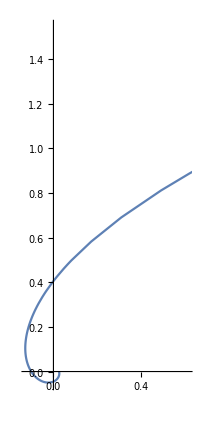

```mathematica
ParametricPlot[
{Cos[t]/t^2,Sin[t]/t^2}
,{t,0,2π}]
```

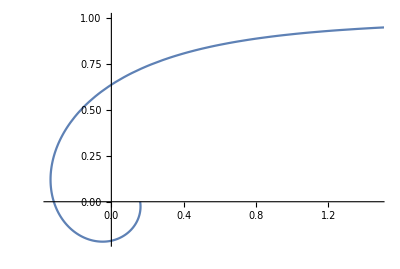

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,2π}]
```

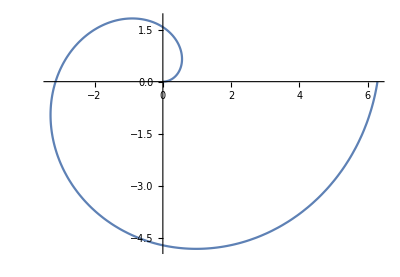

```mathematica
ParametricPlot[
{t Cos[t],t Sin[t]}
,{t,0,2π}]
```

```mathematica
∫_0^1 ∫_0^(2π) {t-a t+a Cos[t],t-a t+a Sin[t]}ⅆtⅆa
```

{π^2,π^2}

```mathematica
Normalize{π^2,π^2}
```

{Normalize π^2,Normalize π^2}

```mathematica
Normalize@{π^2,π^2}
```

{1/(√2),1/(√2)}

```mathematica
Norm@{π^2,π^2}
```

√2 π^2

```mathematica
{(1-a) t+a t,2 (1-a)+3 a}
```

```mathematica
∫_0^1 ∫_0^(2π) {(1-a) t+a t,2 (1-a)+3 a}ⅆtⅆa
```

{2 π^2,5 π}

```mathematica
Norm@{2 π^2,5 π}
```

√(25 π^2+4 π^4)

```mathematica
N[√(25 π^2+4 π^4)]
```

25.2265

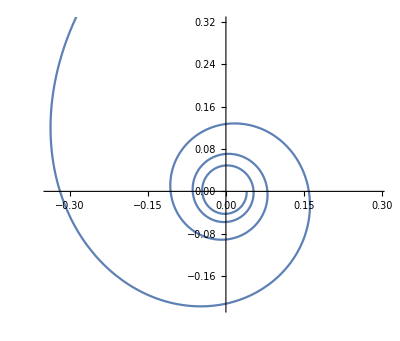

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,8π}]
```

```mathematica
{Cos[t],Sin[t]}.RotationMatrix[θ]
```

{Cos[t] Cos[θ]+Sin[t] Sin[θ],Cos[θ] Sin[t]-Cos[t] Sin[θ]}

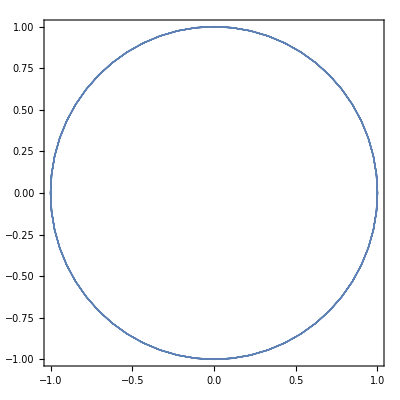

```mathematica
ParametricPlot[
{Cos[t] Cos[θ]+Sin[t] Sin[θ],Cos[θ] Sin[t]-Cos[t] Sin[θ]}
,{t,0,2π},{θ,0,2π}]
```

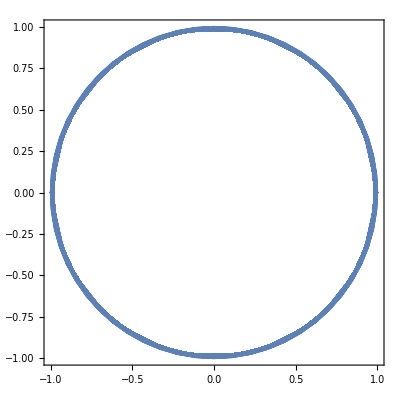

```mathematica
ParametricPlot[
{Cos[t] Cos[θ]+Sin[t] Sin[θ],Cos[θ] Sin[t]-Cos[t] Sin[θ]}
,{t,0,2π},{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{Cos[t] Cos[θ]+Sin[t] Sin[θ],Cos[θ] Sin[t]-Cos[t] Sin[θ]}
,{t,0,2π}],{θ,0,8π}]
```

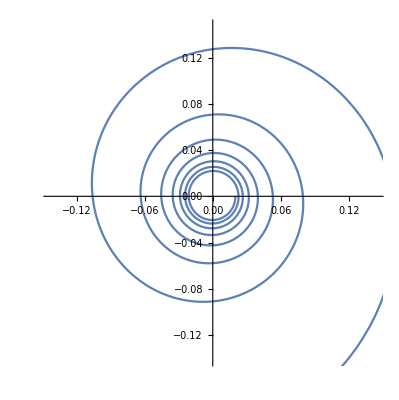

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,16π}]
```

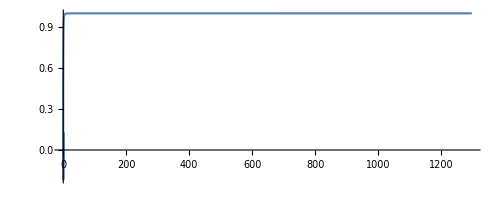

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,16π},PlotRange->Full]
```

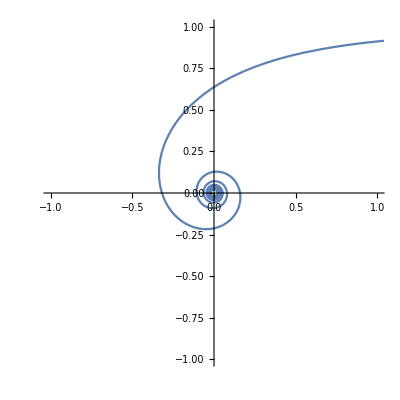

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,16π},PlotRange->{{-1,1},{-1,1}}]
```

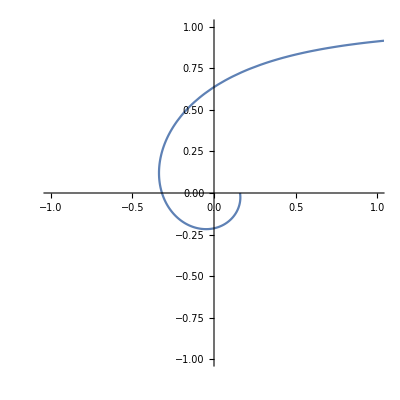

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,2π},PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
(1-a){Cos[t],Sin[t]}+a {Cos[t]/t,Sin[t]/t}
```

{(1-a) Cos[t]+(a Cos[t])/t,(1-a) Sin[t]+(a Sin[t])/t}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) Cos[t]+(a Cos[t])/t,(1-a) Sin[t]+(a Sin[t])/t}
,{t,0,2π}],{a,0,1}]
```

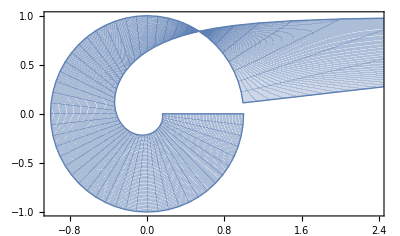

```mathematica
ParametricPlot[
{(1-a) Cos[t]+(a Cos[t])/t,(1-a) Sin[t]+(a Sin[t])/t}
,{t,0,2π},{a,0,1}]
```

```mathematica
Norm@{t-a t+a Cos[t],t-a t+a Sin[t]}
```

√(Abs[t-a t+a Cos[t]]^2+Abs[t-a t+a Sin[t]]^2)

```mathematica
√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)
```

√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)

```mathematica
{(1-a) Cos[t]+(a Cos[t])/t,(1-a) Sin[t]+(a Sin[t])/t}/.a->0
```

{Cos[t],Sin[t]}

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm@{-t+Cos[t],-t+Sin[t]}
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
√((-t+Cos[t])^2+(-t+Sin[t])^2)
```

√((-t+Cos[t])^2+(-t+Sin[t])^2)

```mathematica
FullSimplify[√((-t+Cos[t])^2+(-t+Sin[t])^2)]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

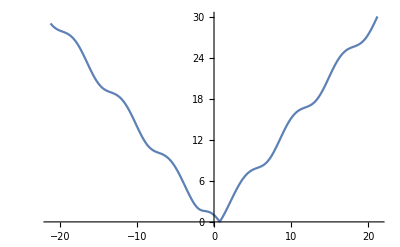

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-21.205750411731103,21.205750411731103}]
```

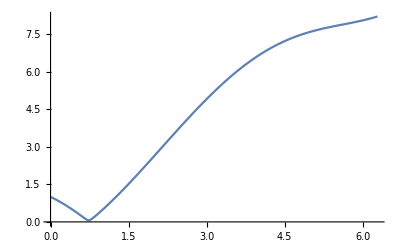

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

```mathematica
FindMinimum[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0}]
```

{0.0647013,{t→0.733196}}

```mathematica
FindMaximum[√(1+2 t^2-2 t (Cos[t]+Sin[t]))∧0≤t≤2π,{t,0}]
```

{1.,{t→0.}}

```mathematica
FindMaximum[√(1+2 t^2-2 t (Cos[t]+Sin[t]))∧0≤t≤2π,{t,5}]
```

{7.59951,{t→5.}}

```mathematica
FindMaximum[√(1+2 t^2-2 t (Cos[t]+Sin[t]))∧0≤t≤2π,{t,2π}]
```

{8.20917,{t→6.28319}}

```mathematica
(1-a){t,t}+a{t,Sin[t]}
```

{(1-a) t+a t,(1-a) t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a t,(1-a) t+a Sin[t]}
,{t,0,2π}],{a,0,1}]
```

```mathematica
With[{f={(1-a) t+a t,(1-a) t+a Sin[t]}},
(f/.0)-(f/.1)
]
```

{ComplexInfinity,ComplexInfinity}

```mathematica
With[{f={(1-a) t+a t,(1-a) t+a Sin[t]}},
(f/. 1)-(f/. 0)
]
```

-({(1-a) t+a t,(1-a) t+a Sin[t]}/.0)+({(1-a) t+a t,(1-a) t+a Sin[t]}/.1)

```mathematica
{(1-a) t+a t,(1-a) t+a Sin[t]}/.a->0
```

{t,t}

```mathematica
{t,Sin[t],
```

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

$Aborted

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
{t,Sin[t]}-{t,t}
```

{0,-t+Sin[t]}

```mathematica
Norm@{0,-t+Sin[t]}
```

Abs[-t+Sin[t]]

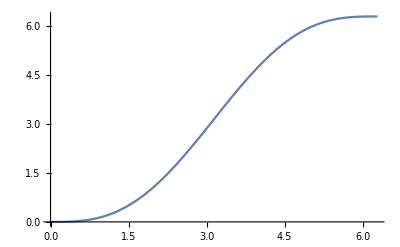

```mathematica
Plot[Abs[-t+Sin[t]],{t,0,2π}]
```

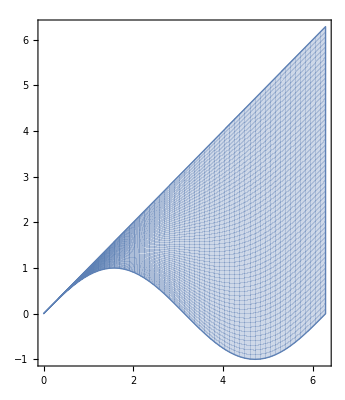

```mathematica
ParametricPlot[
{(1-a) t+a t,(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
∫_0^(2π) tⅆt-∫_0^(2π) Sin[t]ⅆt
```

2 π^2

```mathematica
NIntegrate[Abs[-t+Sin[t]],{t,0,2π}]
```

19.7392

```mathematica
Integrate[Abs[-t+Sin[t]],{t,0,2π}]
```

2 π^2

```mathematica
Integrate[Sin[t],{t,0,2π}]
```

0

```mathematica
Integrate[Abs[Sin[t]],{t,0,2π}]
```

4

```mathematica
Sin[f[x]]
```

Sin[f[x]]

```mathematica
{x,Sin[x]}.RotationMatrix[π/4]
```

{x/(√2)+Sin[x]/(√2),-x/(√2)+Sin[x]/(√2)}

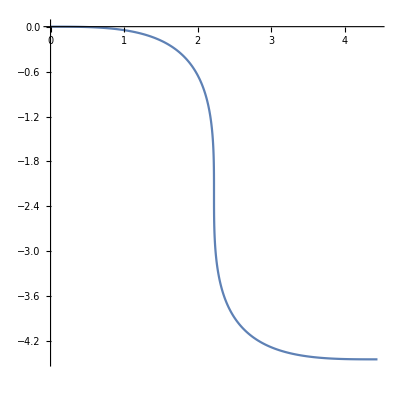

```mathematica
ParametricPlot[
{x/(√2)+Sin[x]/(√2),-x/(√2)+Sin[x]/(√2)}
,{x,0,2π}]
```

```mathematica
ParametricPlot[
{x/(√2)+Sin[x]/(√2),-x/(√2)+Sin[x]/(√2)}
,{x,0,2π}]
```

```mathematica
{x,Sin[x]}.RotationMatrix[2π-π/4]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

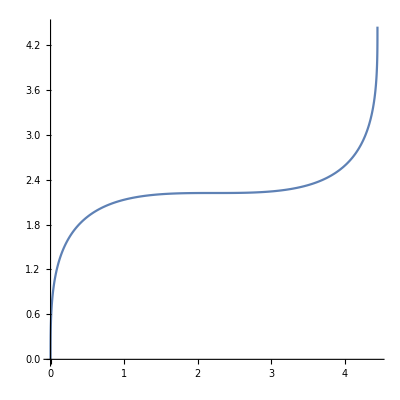

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,0,2π}]
```

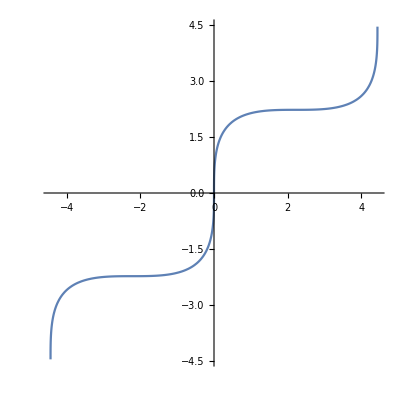

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,-2π,2π}]
```

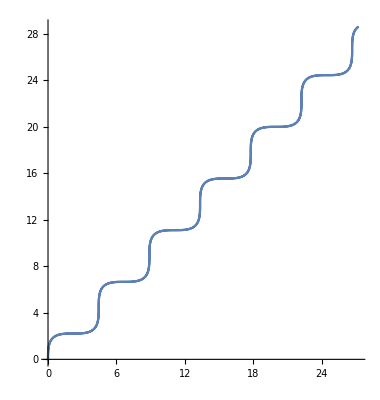

```mathematica
ParametricPlot[
{x^2/(√2)-Sin[x^2]/(√2),x^2/(√2)+Sin[x^2]/(√2)}
,{x,-2π,2π}]
```

```mathematica
(1-a){x,x}+a{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
```

{(1-a) x+a (x/(√2)-Sin[x]/(√2)),(1-a) x+a (x/(√2)+Sin[x]/(√2))}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) x+a (x/(√2)-Sin[x]/(√2)),(1-a) x+a (x/(√2)+Sin[x]/(√2))}
,{x,0,2π}],{a,0,1}]
```

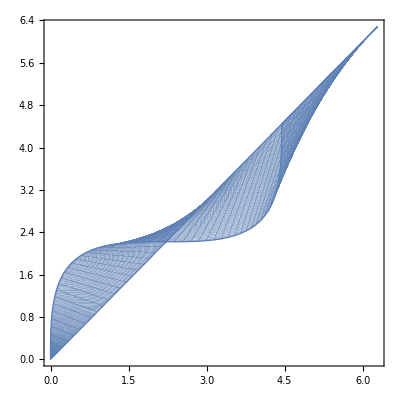

```mathematica
ParametricPlot[
{(1-a) x+a (x/(√2)-Sin[x]/(√2)),(1-a) x+a (x/(√2)+Sin[x]/(√2))}
,{x,0,2π},{a,0,1}]
```

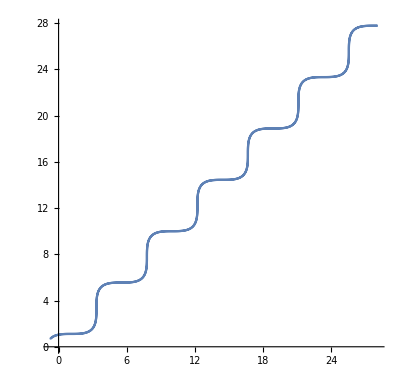

```mathematica
ParametricPlot[
{x^2/(√2)-Cos[x^2]/(√2),x^2/(√2)+Cos[x^2]/(√2)}
,{x,-2π,2π}]
```

```mathematica
Normalize@{1,0}.D[{t,Cos[t]},t]
```

1

```mathematica
FullSimplify[Normalize@{a,b}.{c,d},{a,b,c,d}∈Reals]
```

```mathematica
Inactivate[1]
```

1

```mathematica
Inactivate[a+1]
```

a+1

```mathematica
Inactivate[2+1]
```

2+1

```mathematica
FullSimplify[Normalize@{a,b}.Normalize@{c,d},{a,b,c,d}∈Reals]
```

(a c+b d)/(√((a^2+b^2) (c^2+d^2)))

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))/.{a->1,b->0,c->1,d->1}
```

1/(√2)

```mathematica
{a,b}==1/(√2){c,d}
```

{a,b}=={c/(√2),d/(√2)}

```mathematica
{a,b}==α{c,d}
```

{a,b}=={c α,d α}

```mathematica
FullSimplify[Normali{t,t^2}.{t,t},t∈Reals]
```

Normali t^2 (1+t)

```mathematica
FullSimplify[Normalize@{1,2t}.Normalize@{1,1},t∈Reals]
```

(1+2 t)/(√(2+8 t^2))

```mathematica
FullSimplify[(Normalize@{1,2t}.Normalize@{1,1}){t,t},t∈Reals]
```

{(t (1+2 t))/(√(2+8 t^2)),(t (1+2 t))/(√(2+8 t^2))}

```mathematica
Integrate[{(t (1+2 t))/(√(2+8 t^2)),(t (1+2 t))/(√(2+8 t^2))},t]
```

{(2 (1+t) √(1+4 t^2)-ArcSinh[2 t])/(8 √2),(2 (1+t) √(1+4 t^2)-ArcSinh[2 t])/(8 √2)}

```mathematica
(1+2 t)/(√(2+8 t^2))
```

(1+2 t)/(√(2+8 t^2))

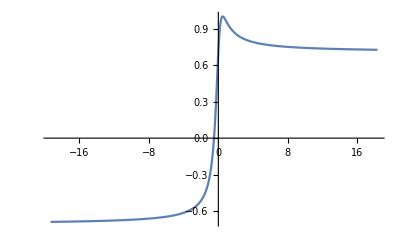

```mathematica
Plot[(1+2 t)/(√(2+8 t^2)),{t,-19.30666666666667,18.30666666666667}]
```

```mathematica
f[a[x],p[x]]
```

f[a[x],p[x]]

```mathematica
f[a[x],p'[x]]
```

f[a[x],p'[x]]

```mathematica
Normalize@{t,0}.Normalize@D[{t,Cos[t]},t]
```

t/(Abs[t] √(1+Abs[Sin[t]]^2))

```mathematica
{a,b}.{c,d}==a c+b d
```

True

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t,Sin[t]},t]
,t∈Reals]
```

(1+Cos[t])/(√(3+Cos[2 t]))

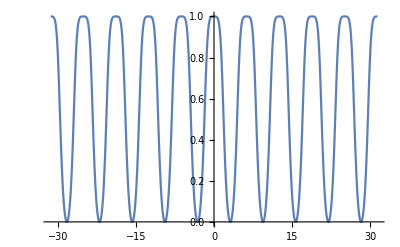

```mathematica
Plot[(1+Cos[t])/(√(3+Cos[2 t])),{t,-10 π,10 π}]
```

```mathematica
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
```

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,t∈Reals]
```

(√2)/(√(3+Cos[2 t]))

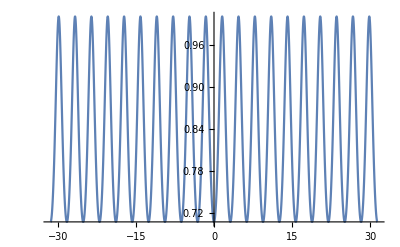

```mathematica
Plot[(√2)/(√(3+Cos[2 t])),{t,-10 π,10 π}]
```

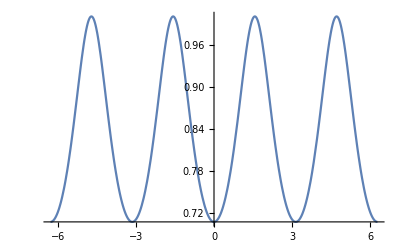

```mathematica
Plot[(√2)/(√(3+Cos[2 t])),{t,-2 π,2 π}]
```

```mathematica
(√2)/(√(3+Cos[2 t]))2t
```

(2 √2 t)/(√(3+Cos[2 t]))

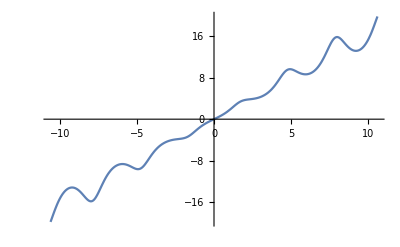

```mathematica
Plot[(2 √2 t)/(√(3+Cos[2 t])),{t,-10.602875205865551,10.602875205865551}]
```

```mathematica
Integrate[(2 √2 t)/(√(3+Cos[2 t])),t]
```

2 √2 ∫t/(√(3+Cos[2 t]))ⅆt

```mathematica
FullSimplify[2 √2 ∫t/(√(3+Cos[2 t]))ⅆt]
```

2 √2 ∫t/(√(3+Cos[2 t]))ⅆt

```mathematica
Table[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,1,10}]
```

{0.76595,1.72844,2.52177,3.26649,4.21693,5.04253,5.77282,6.70065,7.56128,8.2842}

```mathematica
Table[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,1,10,.1}]
```

{0.76595,0.855478,0.948042,1.04339,1.14105,1.24029,1.34023,1.43988,1.53829,1.63467,1.72844,1.81925,1.90697,1.99165,2.07348,2.15272,2.22968,2.30471,2.37816,2.45039,2.52177,2.59264,2.66337,2.7343,2.8058,2.87821,2.9519,3.02723,3.10455,3.1842,3.26649,3.35168,3.43992,3.53124,3.62548,3.72225,3.82093,3.9207,4.02059,4.11962,4.21693,4.31184,4.40391,4.49291,4.57885,4.66184,4.74212,4.81998,4.89577,4.96984,5.04253,5.11422,5.18526,5.25601,5.32681,5.39803,5.47002,5.54313,5.61773,5.69418,5.77282,5.85399,5.93794,6.0249,6.11495,6.20801,6.30378,6.40176,6.50119,6.60115,6.70065,6.79877,6.89475,6.98804,7.07833,7.16553,7.24972,7.3311,7.40993,7.48654,7.56128,7.6345,7.70656,7.77783,7.84865,7.91939,7.99039,8.06201,8.13462,8.20856,8.2842}

```mathematica
DiscretePlot[Table[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,1,10,.1}]]
```

DiscretePlot[Table[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,1,10,0.1}]]

```mathematica
DiscretePlot[Out[283]]
```

DiscretePlot[%283]

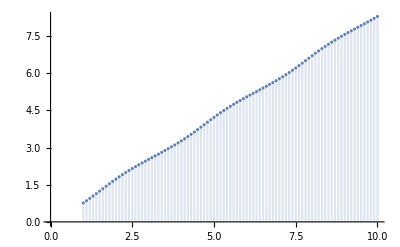

```mathematica
DiscretePlot[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,1,10,.1}]
```

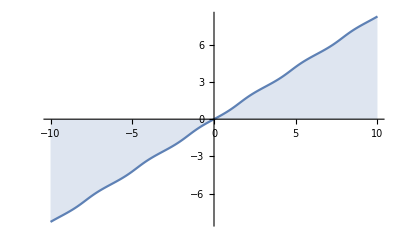

```mathematica
DiscretePlot[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,-10,10,.1}]
```

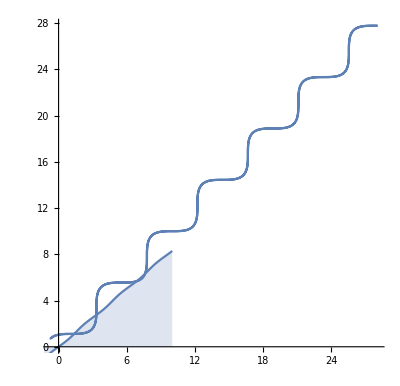

```mathematica
Show[{
ParametricPlot[
{x^2/(√2)-Cos[x^2]/(√2),x^2/(√2)+Cos[x^2]/(√2)}
,{x,-2π,2π}],
DiscretePlot[NIntegrate[(√2)/(√(3+Cos[2 t])),{t,0,a}],{a,-10,10,.1}]
}]
```

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
FullForm[Dt[Dt[f[x]]]]
```

Plus[Times[Dt[Dt[x]],Derivative[1][f][x]],Times[Power[Dt[x],2],Derivative[2][f][x]]]

```mathematica
Solve[Dt[Dt[f[x]]]==(√2)/(√(3+Cos[2 t])),f[x]]
```

{}

```mathematica
Dt[Dt[f[x]]]==(√2)/(√(3+Cos[2 t]))
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==(√2)/(√(3+Cos[2 t]))

```mathematica
Dt[Dt[f[t]]]==(√2)/(√(3+Cos[2 t]))
```

Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(√2)/(√(3+Cos[2 t]))

```mathematica
Dt[Dt[t]] f'[t]+Dt[t]^2 f''[t]==(√2)/(√(3+Cos[2 t]))/.Dt[t]->1
```

f''[t]==(√2)/(√(3+Cos[2 t]))

```mathematica
DSolve[f''[t]==(√2)/(√(3+Cos[2 t])),{f[t]},{t}]
```

{{f[t]→C[1]+t C[2]+EllipticF[K[1],1/2]/(√2)K[1]1t}}

```mathematica
Elliptic
```

```mathematica
Dt[f[t]]==(√2)/(√(3+Cos[2 t]))
```

Dt[t] f'[t]==(√2)/(√(3+Cos[2 t]))

```mathematica
f'[t]==(√2)/(√(3+Cos[2 t]))
```

f'[t]==(√2)/(√(3+Cos[2 t]))

```mathematica
DSolve[f'[t]==(√2)/(√(3+Cos[2 t])),{f[t]},{t}]
```

{{f[t]→C[1]+EllipticF[t,1/2]/(√2)}}

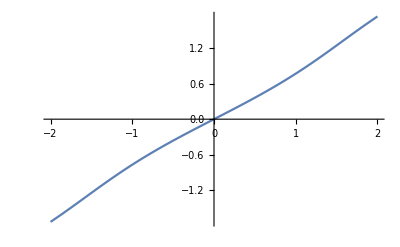

```mathematica
Plot[EllipticF[t,1/2]/(√2),{t,-2,2}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,t∈Reals]
```

(1+2 t+(-1+2 t) Cos[t])/(√((1+4 t^2) (3+Cos[2 t])))

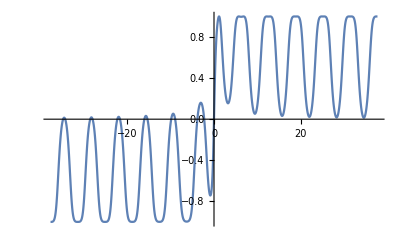

```mathematica
Plot[(1+2 t+(-1+2 t) Cos[t])/(√((1+4 t^2) (3+Cos[2 t]))),{t,-37.69911184307752,37.69911184307752}]
```

```mathematica
(1+2 t+(-1+2 t) Cos[t])/(√((1+4 t^2) (3+Cos[2 t])))2t
```

(2 t (1+2 t+(-1+2 t) Cos[t]))/(√((1+4 t^2) (3+Cos[2 t])))

```mathematica
Integrate[(2 t (1+2 t+(-1+2 t) Cos[t]))/(√((1+4 t^2) (3+Cos[2 t]))),t]
```

2 ∫(t (1+2 t+(-1+2 t) Cos[t]))/(√((1+4 t^2) (3+Cos[2 t])))ⅆt

```mathematica
Solve[(2 t (1+2 t+(-1+2 t) Cos[t]))/(√((1+4 t^2) (3+Cos[2 t])))==a(√2)/(√(3+Cos[2 t])),a]
```

{{a→(√2 t (1+2 t+(-1+2 t) Cos[t]) √(3+Cos[2 t]))/(√((1+4 t^2) (3+Cos[2 t])))}}

```mathematica
Integrate[(√2 t (1+2 t+(-1+2 t) Cos[t]) √(3+Cos[2 t]))/(√((1+4 t^2) (3+Cos[2 t]))),t]
```

√2 ∫(t (1+2 t+(-1+2 t) Cos[t]) √(3+Cos[2 t]))/(√((1+4 t^2) (3+Cos[2 t])))ⅆt

```mathematica
FullSimplify[
Normalize@D[{t,f[t]},t].Normalize@D[{t,Sin[t]},t]==Sin[t]
,t∈Reals]
```

√((1+Abs[f'[t]]^2) (1+Cos[t]^2)) Sin[t]==1+Cos[t] f'[t]

```mathematica
FullSimplify[
Normalize@D[{t,f[t]},t].Normalize@D[{t,Sin[t]},t]==Sin[t]
,{t,f'[t]}∈Reals]
```

1+Cos[t] f'[t]==Sin[t] √((1+Cos[t]^2) (1+f'[t]^2))

```mathematica
DSolve[1+Cos[t] f'[t]==Sin[t] √((1+Cos[t]^2) (1+f'[t]^2)),{f[t]},{t}]
```

{{f[t]→C[1]+1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]])},{f[t]→C[1]+1/10 (-4 √5 ArcTanh[(1+2 Sin[t])/(√5)]-(-5+√5) Log[1-√5+2 Sin[t]]+(5+√5) Log[1+√5+2 Sin[t]])}}

```mathematica
Plot[1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]]),{t,-1,1}]
```

-Graphics-

```mathematica
FullSimplify[1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]]),t∈Reals∧0≤t≤2π]
```

1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]])

```mathematica
TrigReduce[1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]])]
```

1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]-5 Log[1-√5-2 Sin[t]]+√5 Log[1-√5-2 Sin[t]]-5 Log[1+√5-2 Sin[t]]-√5 Log[1+√5-2 Sin[t]])

```mathematica
Plot[1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]-5 Log[1-√5-2 Sin[t]]+√5 Log[1-√5-2 Sin[t]]-5 Log[1+√5-2 Sin[t]]-√5 Log[1+√5-2 Sin[t]]),{t,0,2π}]
```

-Graphics-

```mathematica
DiscretePlot[NIntegrate[1/10 (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]]),{t,0,a}],{a,-10,10,.1}]
```

-Graphics-

```mathematica
Tanh[x]
```

Tanh[x]

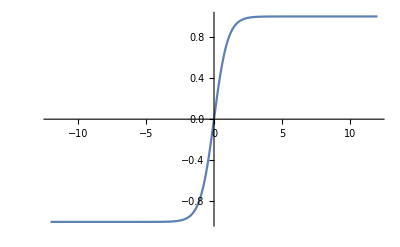

```mathematica
Plot[Tanh[x],{x,-12.,12.}]
```

```mathematica
ArcTanh[x]
```

ArcTanh[x]

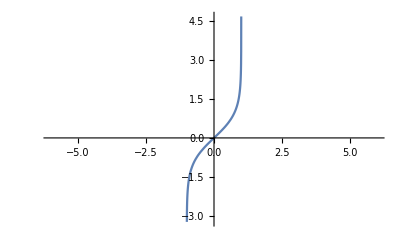

```mathematica
Plot[ArcTanh[x],{x,-6.,6.}]
```

```mathematica
DiscretePlot[ (4 √5 ArcTanh[(1-2 Sin[t])/(√5)]+(-5+√5) Log[1-√5-2 Sin[t]]-(5+√5) Log[1+√5-2 Sin[t]])/10,{t,-10,10,.1}]
```

-Graphics-

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]==Normalize@D[{t,f[t]},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,t∈Reals]
```

(√2)/(√(3+Cos[2 t]))==(1-Cos[t]+(1+Cos[t]) f'[t])/(√((1+Abs[f'[t]]^2) (3+Cos[2 t])))

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]==Normalize@D[{t,f[t]},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,{t,f'[t]}∈Reals]
```

(√2)/(√(3+Cos[2 t]))==(1-Cos[t]+(1+Cos[t]) f'[t])/(√((3+Cos[2 t]) (1+f'[t]^2)))

```mathematica
DSolve[(√2)/(√(3+Cos[2 t]))==(1-Cos[t]+(1+Cos[t]) f'[t])/(√((3+Cos[2 t]) (1+f'[t]^2))),{f[t]},{t}]
```

{{f[t]→t+C[1]},{f[t]→t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]+C[1]}}

```mathematica
DiscretePlot[ t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))],{a,-10,10,.1}]
```

-Graphics-

```mathematica
Plot[ t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))],{a,-10,10,}]
```

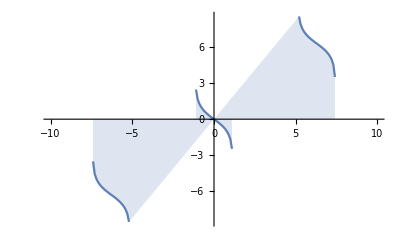

```mathematica
DiscretePlot[ t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))],{t,-10,10,.1}]
```

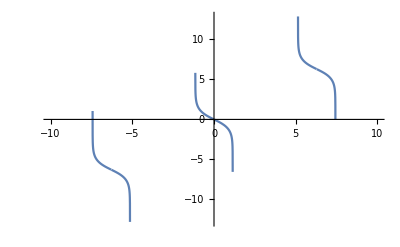

```mathematica
Plot[ t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))],{t,-10,10}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,{t,f'[t]}∈Reals]
```

-(√2)/(√(3+Cos[2 t]) Sign[-1+4 Cos[t]+Cos[2 t]])

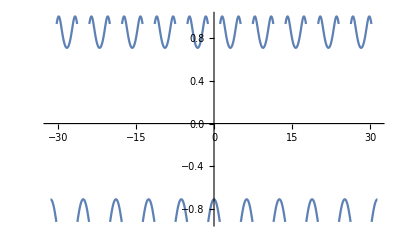

```mathematica
Plot[-(√2)/(√(3+Cos[2 t]) Sign[-1+4 Cos[t]+Cos[2 t]]),{t,-10 π,10 π}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,{t,f'[t]}∈Reals]
```

(√2)/(√(3+Cos[2 t]))

```mathematica
Plot[(√2)/(√(3+Cos[2 t])),{t,-10 π,10 π}]
```

-Graphics-

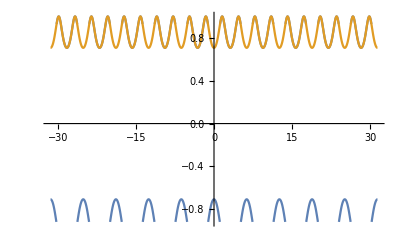

```mathematica
Plot[{
-(√2)/(√(3+Cos[2 t]) Sign[-1+4 Cos[t]+Cos[2 t]]),
(√2)/(√(3+Cos[2 t]))
},{t,-10 π,10 π}]
```

```mathematica
ParametricPlot[
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}
,{x,-2π,2π}]
```

-Graphics-

```mathematica
Plot[ t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))],{t,-10,10}]
```

-Graphics-

```mathematica
t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]
```

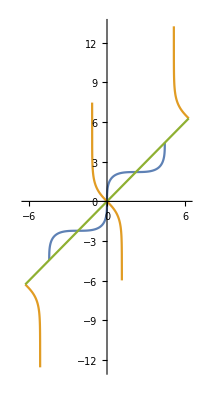

```mathematica
ParametricPlot[{
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},
{t,t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]},
{t,t}
},{t,-2π,2π}]
```

```mathematica
Tan[θ]Cos[θ]
```

Sin[θ]

```mathematica
α 2^x==3^x
```

2^x α==3^x

```mathematica
Solve[2^x α==3^x,α,Reals]
```

{{α→(3/2)^x}}

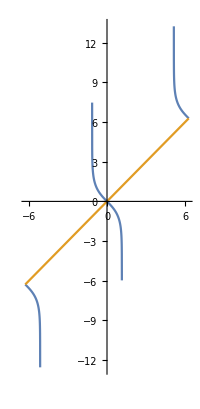

```mathematica
ParametricPlot[{
{t,t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]},
{t,t}
},{t,-2π,2π}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f'[t],g'[t]},t]==2^x
,{t,f'[t],g'[t]}∈Reals]
```

(f''[t]+2 t g''[t])/(√((1+4 t^2) (Abs[f''[t]]^2+Abs[g''[t]]^2)))==2^x

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f'[t],g'[t]},t]==2^x
,{t,f'[t],g'[t],f''[t],g''[t]}∈Reals]
```

(f''[t]+2 t g''[t])/(√((1+4 t^2) (f''[t]^2+g''[t]^2)))==2^x

```mathematica
DSolve[(f''[t]+2 t g''[t])/(√((1+4 t^2) (f''[t]^2+g''[t]^2)))==2^x,{f[t],g[t]},{t,x}]
```

DSolve[(f''[t]+2 t g''[t])/(√((1+4 t^2) (f''[t]^2+g''[t]^2)))==2^x,{f[t],g[t]},{t,x}]

```mathematica
(√2)/(√(3+Cos[2 t]))
```

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f'[t],g'[t]},t]==(√2)/(√(3+Cos[2 t]))
,{t,f'[t],g'[t],f''[t],g''[t]}∈Reals]
```

(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2

```mathematica
DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,{f[t],g[t]},{t}]
```

DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,{f[t],g[t]},{t}]

```mathematica
Solve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,f''[t],Reals]
```

Solve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,f''[t],ℝ]

```mathematica
DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,f''[t],t]
```

DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,f''[t],t]

```mathematica
DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,{f''[t]},{t}]
```

DSolve[(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2,{f''[t]},{t}]

```mathematica
x/(√2)-Sin[x]/(√2)==x/(√2)+Sin[x]/(√2)
```

x/(√2)-Sin[x]/(√2)==x/(√2)+Sin[x]/(√2)

```mathematica
Reduce[x/(√2)-Sin[x]/(√2)==x/(√2)+Sin[x]/(√2)]
```

Sin[x]==0

```mathematica
Solve[x/(√2)-Sin[x]/(√2)==α x/(√2)+Sin[x]/(√2),α,Reals]
```

{{α→ConditionalExpression[(x-2 Sin[x])/x,x>0||x<0]}}